```mathematica
Remove["Global`*"]
messagebak=$Messages;
$Messages=Null;
imagesize1=Small;
imagesize2=Medium;
fontsize1=10;
fonstsize2=14;
(*PRIMARY PLOTTING ROUTINE*)
MP[f_,title_]:=Plot[f,{z,.1,5},PlotRange->All(*,PlotStyle->{Thick,Black},AxesStyle->Thick*),PlotLabel->Style[title,Bold,fontsize1],AspectRatio->1,ImageSize->imagesize1,PlotTheme->"Detailed",PlotLegends->None]
(*SECONDARY PLOTTING ROUTINE -- PLOTS MULTIPLE COSMOLOGICAL PARAMETERS -- INPUT IS FUNCTION TO PLOT*)
(*TO PLOT A DIFFERENT SET OF FUNCTIONS CHANGE THIS ROUTINE TO MATCH WHAT WILL BE PLOTTED*)
MPMULT[fr_,fda_,fdl_,fdv_,ft_]:=TableForm[{{MP[fr,"Comoving Distance  D_C/D_H"],MP[fda,"Angular Diameter Distance D_A/D_H"],MP[fdl,"Distance Modulus"],MP[fdv,"Comoving Volume V_C/D_H^3"],MP[ft,"Age of Universe  t_age(Gyr)"]}}]
(*******************************************************************************************)

(*OVERLAY PLOT ROUTINES -- CURRENTLY SET UP TO PLOT 3 FUNCTIONS WITH THREE COLORS*)
(*LIMITATIONS ARE DUE TO PLOTSTYLE . REMOVE PLOTSTYLE TO PLOT ARBITRARY NUMBER OF PLOTS*)
(*ANOTHER LIMITATION IS PLOTLEGENDS. A SIMPLE MODIFICATION IS NECESSARY FOR GENERALITY IN THE CASE*)
(*******************************************************************************************)

plot3noleg[f_,title_,Label_]:=Plot[f,{z,.1,9},PlotRange->All,(*PlotStyle->{{Thick,CMYKColor[0,1,1,0]}, {Thick,CMYKColor[1,0,1,0]},{Thick,CMYKColor[1,1,0,0]}},*)PlotLabel->Style[title,"Label",10](*,AxesStyle->Thick,Frame->True,FrameTicksStyle->12*),AspectRatio->1,AxesLabel->{Style["z","Label",14],Style[Label,"Label",fonstsize2]},PlotLegends->None,FrameLabel->{Style["z","Label",fonstsize2],Style[Label,"Label",fonstsize2]},ImageSize->imagesize2,GridLines->Automatic,PlotTheme->"Detailed"]

plot3leg[f_,title_,Label_]:=Plot[f,{z,.1,9},PlotRange->All(*,PlotStyle->{{Thick,CMYKColor[0,1,1,0]},{Thick,CMYKColor[1,0,1,0]},{Thick,CMYKColor[1,1,0,0]}}*),PlotLabel->Style[title,"Label",fonstsize2](*,AxesStyle->Thick,Frame->True,FrameTicksStyle->12*),AspectRatio->1,PlotLegends->{"(Ωm,ΩΛ) = (1,0)","(Ωm,ΩΛ) = (0.3,0)","(Ωm,ΩΛ) = (0.3,0.7)"},AxesLabel->{Style["z","Label",14],Style[Label,"Label",fonstsize2]},FrameLabel->{Style["z","Label",fonstsize2],Style[Label,"Label",10]},ImageSize->imagesize2,GridLines->Automatic,PlotTheme->"Detailed"]


logplot3noleg[f_,title_,Label_]:=LogLinearPlot[f,{z,.1,9},PlotRange->All(*,PlotStyle->{{Thick,CMYKColor[0,1,1,0]},{Thick,CMYKColor[1,0,1,0]},{Thick,CMYKColor[1,1,0,0]}}*),PlotLabel->Style[title,"Label",14](*,AxesStyle->Thick,Frame->True,FrameTicksStyle->12*),AspectRatio->1,PlotLegends->None,AxesLabel->{Style["z (log_10 scale)","Label",fonstsize2],Style[Label,"Label",fonstsize2]},FrameLabel->{Style["z (log_10 scale)","Label",fonstsize2],Style[Label,"Label",10]},ImageSize->imagesize2,GridLines->Automatic,PlotTheme->"Detailed"]

logplot3leg[f_,title_,Label_]:=LogLinearPlot[f,{z,.1,9},PlotRange->All(*,PlotStyle->{{Thick,CMYKColor[0,1,1,0]},{Thick,CMYKColor[1,0,1,0]},{Thick,CMYKColor[1,1,0,0]}}*),PlotLabel->Style[title,"Label",fonstsize2](*,AxesStyle->Thick,Frame->True,FrameTicksStyle->12*),AspectRatio->1,PlotLegends->{"(Ωm,ΩΛ) = (1,0)","(Ωm,ΩΛ) = (0.3,0)","(Ωm,ΩΛ) = (0.3,0.7)"},AxesLabel->{Style["z (log_10 scale)","Label",10],Style[Label,"Label",fonstsize2]},FrameLabel->{Style["z (log_10 scale)","Label",14],Style[Label,"Label",fonstsize2]},ImageSize->imagesize2,GridLines->Automatic,PlotTheme->"Detailed"]

PrintCos[m_,Λ_,x_]:=Print[" (Ωm,ΩΛ) = (",m,",",Λ,") universe ",x]
```

Problem 1

(Ωm,ΩΛ) = (1.,0.) universe is Einstein-de Sitter Universe

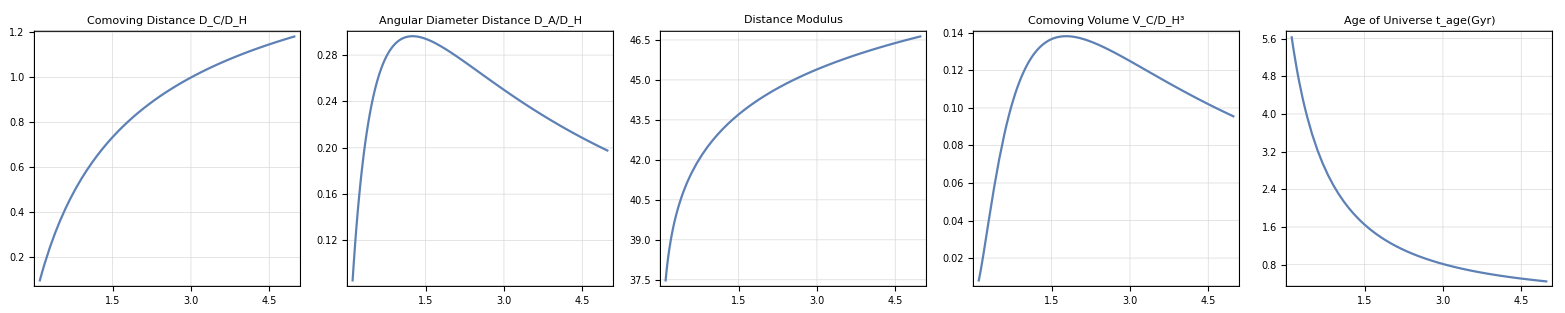

(Ωm,ΩΛ) = (0.3,0) universe is the low matter density universe

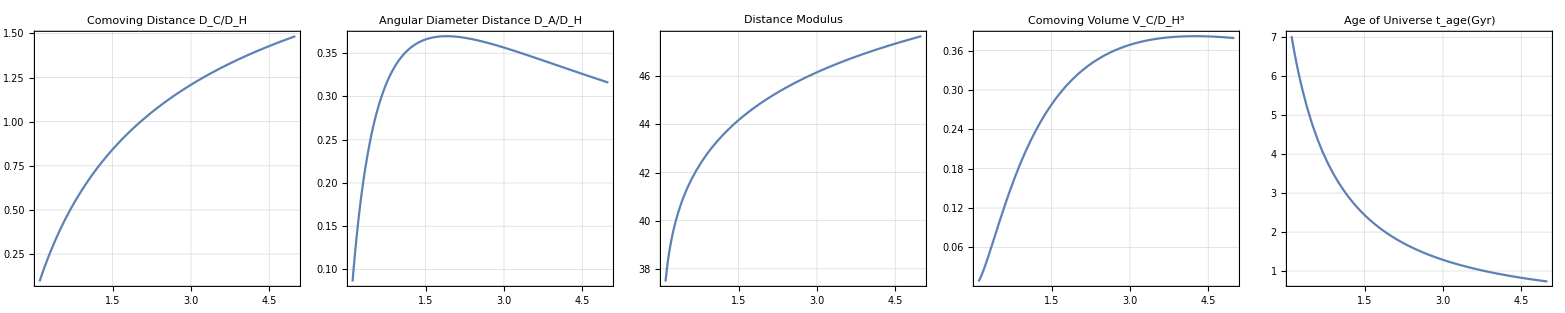

(Ωm,ΩΛ) = (0.3,0.7) universe is the matter-lambda universe

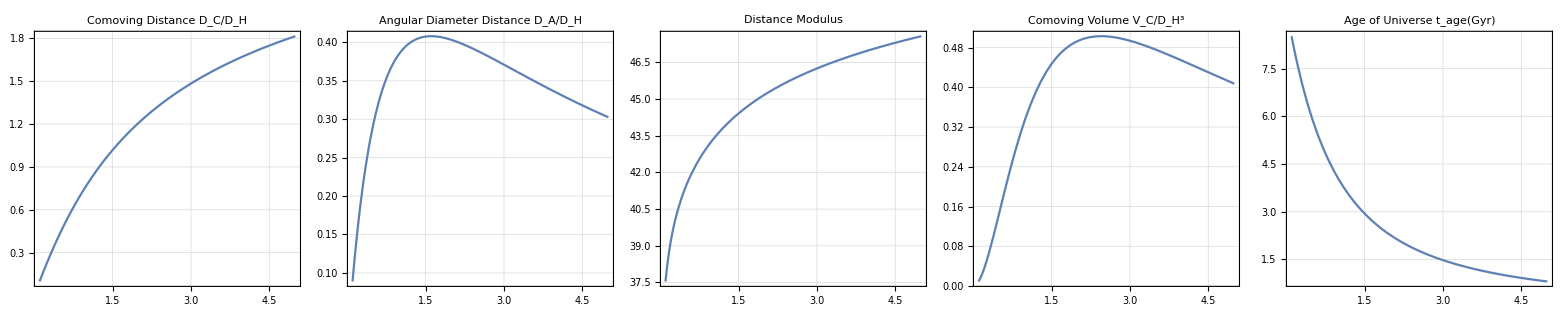

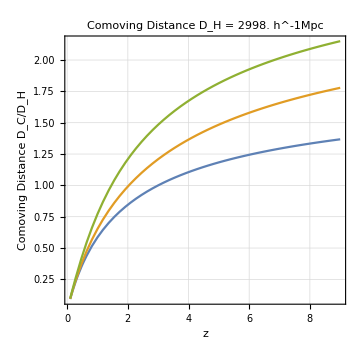
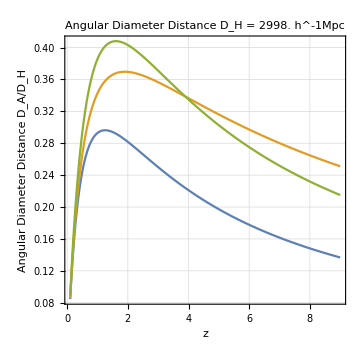
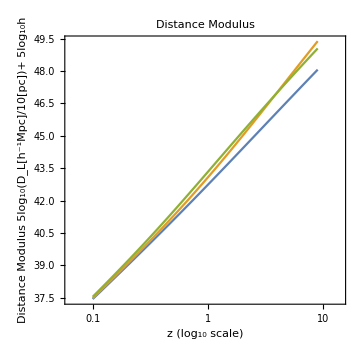
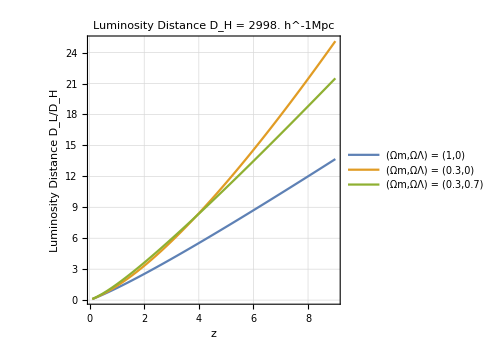
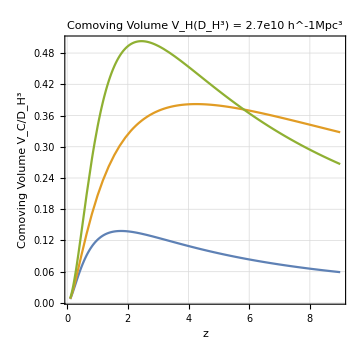
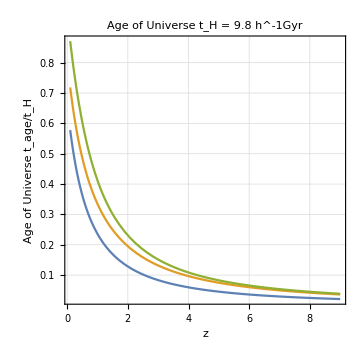
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
(*** NOTES ON UNITS ***)
(*** S[z] is scaled in Mpc=10^6 pc therefore DM=5Subscript[Log, 10][Subscript[D, L]/10pc]-> 5Log[Subscript[D, L]]+25 ***)
(*** Since distance is in h^-1 Mpc  DM=5 Subscript[Log, 10] Subscript[D, L] +25 + 5 Subscript[Log, 10] h*)
(*General Cosmological Relations for Matter, Vacuum Energy, Curvature Universe*)
H[z_]  :=  Ho Sqrt[Ωm (1+z)^3+Ωr (1+z)^2+ΩΛ](*Freidmann Equation*)
(*r[z_]:=Integrate[c/H[ζ],{ζ,0,z},Assumptions->{z≥0}];*) (*comoving distance in General*)
DA[z_]:=S[z]/(1+z) (*unitless angular diameter distance *)
DM[z_]:=5 Log10[ S[z] (1+z)]+25+5Log10[h] (*distance modulus with Subscript[D, L] in h^-1 Mpc *)
DL[z_]:=S[z](1+z)(*Luminosity Distance*)
VC[z_]:= c S[z]^2/H[z](*Comoving Volume per steradian per unit redshift*)
t[z_,hub_]  :=Ho  NIntegrate[((1+ζ)hub)^(-1),{ζ,z,Infinity}(*,Assumptions->{z≥0}*)](*in h^-1 Gyr*)
(*t[z_]    =1;*)(*UNCOMMENT THIS TO RUN PROGRAM FASTER. IT CAUSES TIME NOT TO BE CALCULATED*)
Ωo:=Ωm+ΩΛ 
Ωr:=1-Ωo
Rc:=(√-k c)/(Ho √(1-Ωo))
(*Matter Only *)
Smatter[z_]:=(2 c)/(Ho Ωo^2(1+z))(Ωo z+(Ωo-2)((Ωo z+1)^(1/2)-1))
rmatter[0,z_]:=Smatter[z]
rmatter[-1,z_]:=Rc ArcSinh[(Smatter[z]/Rc)]
rmatter[1,z_]:=Rc ArcSin[(Smatter[z]/Rc)]
(*Matter and Lambda *)
xmatterlambda[z_]:=ΩΛ/(Ωm(1+z)^3+ΩΛ)
rmatterlambda[z_]:=c/(3 Ho Ωm^(1/3) ΩΛ^(1/6))(Beta[xmatterlambda[0],1/6,1/3]-Beta[xmatterlambda[z],1/6,1/3])
Smatterlambda[0,z_]:=rmatterlambda[z]
Smatterlambda[-1,z_]:=Rc Sinh[rmatterlambda[z]/Rc]
Smatterlambda[1,z_]:=Rc Sin[rmatterlambda[z]/Rc]
(***********************************Constants*******************************)
c=(2.998*10^5);(*c=306.4 ;*)(*Mpc/Gyr*)h=1;Ho=100  ;DH=c/Ho (*h^-1 Mpc*);tH=9.78 (*h^-1 Gyr*);VH=DH^3;
(****************************************************************************)


(*PLOT INDIVIDUAL PLOTS FOR EACH COSMOLOGY*)
(***************************************************************************)
Print[""]

(*Begin numerical calculations*)
(*** PLOTS FOR INDIVIDUAL COSMOLOGIES ***)
(****************************************************************************)
(***************************EINSTEIN-DE SITTER******************************)
Ωm=1.0;ΩΛ=0.0;k:=Sign[-Ωr];
S[z_]=Smatter[z];S1[z_]=S[z];H1[z_]=N[H[z]]; 

PrintCos[Ωm,ΩΛ,"is Einstein-de Sitter Universe"];

r1[z_]=(1/DH)rmatter[k,z];da1[z_]=(1/DH)DA[z];dm1[z_]=DM[z];dv1[z_]=(1/VH)VC[z];t1[z_]=t[z,H1[ζ]];dl1[z_]=(1/DH)DL[z];

Print[MPMULT[r1[z],da1[z],dm1[z],dv1[z],tH t1[z]]];
(****************************************************************************)
(***************************LOW MATTER DENSITY******************************)
Ωm=0.3;ΩΛ=0;k:=Sign[-Ωr];
S[z_]=Smatter[z];S2[z_]=S[z];H2[z_]=N[H[z]];

PrintCos[Ωm,ΩΛ,"is the low matter density universe"];

r2[z_]=(1/DH)rmatter[k,z];da2[z_]=(1/DH)DA[z];dm2[z_]=DM[z];dv2[z_]=(1/VH)VC[z];t2[z_]=t[z,H2[ζ]];dl2[z_]=(1/DH)DL[z];

Print[MPMULT[r2[z],da2[z],dm2[z],dv2[z],tH t2[z]]];
(****************************************************************************)
(*************************************MATTER & LAMBDA***********************)
Ωm=0.3;ΩΛ=0.7;k:=Sign[-Ωr];
S[z_]=Smatterlambda[k,z];S3[z_]=S[z];H3[z_]=N[H[z]];

PrintCos[Ωm,ΩΛ,"is the matter-lambda universe"];

r3[z_]=(1/DH)rmatterlambda[z];da3[z_]=(1/DH)DA[z];dm3[z_]=DM[z];dv3[z_]=(1/VH)VC[z];t3[z_]=Evaluate[t[z,H3[ζ]]];dl3[z_]=(1/DH)DL[z];

Print[MPMULT[r3[z],da3[z],dm3[z],dv3[z],tH t3[z]]];
(****************************************************************************)

(*** COMPARATIVE PLOTS FOR DIFFERENT COSMOLOGIES ***)
pdh:=plot3noleg[{r1[z],r2[z],r3[z]},"Comoving Distance   D_H = "<>ToString[NumberForm[c/Ho,4]]<>" h^-1Mpc","Comoving Distance  D_C/D_H"]
pda:=plot3noleg[{da1[z],da2[z],da3[z]},"Angular Diameter Distance   D_H = "<>ToString[NumberForm[c/Ho,4]]<>" h^-1Mpc","Angular Diameter Distance D_A/D_H"]
pdm:=logplot3noleg[{dm1[z],dm2[z],dm3[z]},"Distance Modulus","Distance Modulus  5log_10(D_L[h^-1Mpc]/10[pc])+ 5log_10h"]
pvc:=plot3noleg[{dv1[z],dv2[z],dv3[z]},"Comoving Volume   V_H(D_H^3) = "<>ToString[ScientificForm[(c/Ho)^3,2,NumberFormat->(SequenceForm[#1,"e",#3]&)]]<>" h^-1Mpc^3","Comoving Volume V_C/D_H^3"]
pta:=plot3noleg[{t1[z],t2[z],t3[z]},"Age of Universe   t_H = "<>ToString[ScientificForm[(1/Ho)*978.5,2]]<> " h^-1Gyr","Age of Universe t_age/t_H"]
pdl:=plot3leg[{dl1[z],dl2[z],dl3[z]},"Luminosity Distance   D_H = "<>ToString[NumberForm[c/Ho,4]]<>" h^-1Mpc","Luminosity Distance D_L/D_H"]
Print[TableForm[{{pdh,pda},{pdm,pdl},{pvc,pta}}]]
```

Problem 2

```mathematica
mR=10;
FR=3080 10^(-mR/2.5) (*Jansky*);
z1=z/.Last[Solve[DH dl1[z]==10 h^-1 ,z]];
z2=z/.Last[Solve[DH dl2[z]==10 h^-1 ,z]];
z3=z/.Last[NMinimize[{Abs[DH dl3[z]-10 h^-1] ,{0<z,z∈Reals}},z]];
Print[""]
Print["D_L @ z_o is 10 h^-1Mpc"]
DH dl1[z1];
DH dl2[z2];
DH dl3[z3];
Print["R-band Luminosity"]
Print["Ωm=1. ΩΛ=0. universe L_R = ",L1=FR*4π (DH dl1[z1])^2," Jy"]
Print["Ωm=.3 ΩΛ=0. universe L_R = ",L2=FR*4π (DH dl2[z2])^2," Jy"]
Print["Ωm=.3 ΩΛ=.7 universe L_R = ",L3=FR*4π (DH dl3[z3])^2," Jy"]
Print["Move galaxy back. R-band emission has not changed, \n but observer sees it redshifted (z~1.75) into K-Band \n We observe (1+z)L/dl^2 \n 1/(1+z)due to longer wavelenght <-> lower freq"]
zp=1.75;
Print["K band flux observer sees"]
Print["Ωm=1. ΩΛ=0. universe F_K = ",FK1=(1+zp)L1/(4π (DH dl1[zp])^2)," Jy"]
Print["Ωm=1. ΩΛ=0. universe F_K = ",FK2=(1+zp)L2/(4π (DH dl2[zp])^2)," Jy"]
Print["Ωm=1. ΩΛ=0. universe F_K = ",FK3=(1+zp)L3/(4π (DH dl3[zp])^2)," Jy"]
Print["Convert to mag"]
Print["Ωm=1. ΩΛ=0. universe m_K = ",mK1=-2.5 Log10[FK1/640]]
Print["Ωm=.3 ΩΛ=0. universe m_K = ",mK2=-2.5 Log10[FK2/640]]
Print["Ωm=.3 ΩΛ=.7 universe m_K = ",mK3=-2.5 Log10[FK3/640]]
```

D_L @ z_o is 10 h^-1Mpc

R-band Luminosity

Ωm=1. ΩΛ=0. universe L_R = 387.044 Jy

Ωm=.3 ΩΛ=0. universe L_R = 387.044 Jy

Ωm=.3 ΩΛ=.7 universe L_R = 387.044 Jy

Move galaxy back. R-band emission has not changed, 
 but observer sees it redshifted (z~1.75) into K-Band 
 We observe (1+z)L/dl^2 
 1/(1+z)due to longer wavelenght <-> lower freq

K band flux observer sees

Ωm=1. ΩΛ=0. universe F_K = 1.9768×10^-6 Jy

Ωm=1. ΩΛ=0. universe F_K = 1.20861×10^-6 Jy

Ωm=1. ΩΛ=0. universe F_K = 9.93312×10^-7 Jy

Convert to mag

Ωm=1. ΩΛ=0. universe m_K = 21.2755

Ωm=.3 ΩΛ=0. universe m_K = 21.8097

Ωm=.3 ΩΛ=.7 universe m_K = 22.0227

Problem 3

```mathematica
𝓃=.01;
ang=(π/180)^2;
dz=1.8-1.7;
Print[""]
Print["Ωm=1. ΩΛ=0. universe N_galin (1°)^2 and Δz=.1 : ",𝓃 ang c(S1[1.75]^2)dz/H1[1.75] //N ](*Integrate using approximation*)
Print["Ωm=.3 ΩΛ=0. universe  N_galin (1°)^2 and Δz=.1: ",𝓃 ang c(S2[1.75]^2)dz/H2[1.75] //N]
Print["Ωm=.3 ΩΛ=.7 universe  N_galin (1°)^2 and Δz=.1: ",𝓃 ang c(S3[1.75]^2)dz/H3[1.75] //N]

VH NIntegrate[ 𝓃 dv1[z]ang,{z,1.7,1.8}];
VH NIntegrate[ 𝓃 dv2[z]ang,{z,1.7,1.8}];
VH NIntegrate[ 𝓃 dv3[z]ang,{z,1.7,1.8}] ;
```

Ωm=1. ΩΛ=0. universe N_galin (1°)^2 and Δz=.1 : 1134.6

Ωm=.3 ΩΛ=0. universe  N_galin (1°)^2 and Δz=.1: 2492.01

Ωm=.3 ΩΛ=.7 universe  N_galin (1°)^2 and Δz=.1: 3909.02

Problem 4

```mathematica
zo=1.75;
dθ=40/206265 (*40"*);
dz=0.003;
z1=zo-dz/2;
z2=zo+dz/2;
Print[""]
Print["Transverse Proper Distance at t(z=1.75)"]
Print[lt1=S1[zo]dθ]
Print[lt2=S2[zo]dθ]
Print[lt3=S3[zo]dθ]
Print["Radial Proper Distance at t(z=1.75)"]
Print[lr1=c dz/H1[zo]]
Print[lr2=c dz/H2[zo]]
Print[lr3=c dz/H3[zo]]
Print["Proper Distance Between Sources"]
Print[ √(1/(1+zo)^2(lt1^2+lr1^2))//N]
Print[√(1/(1+zo)^2(lt2^2+lr2^2))//N]
Print[√(1/(1+zo)^2(lt3^2+lr3^2))//N]
```

Transverse Proper Distance at t(z=1.75)

0.461596

0.590337

0.651179

Radial Proper Distance at t(z=1.75)

1.97221

2.64841

3.41431

Proper Distance Between Sources

0.736549

0.986693

1.26394

Problem 5

```mathematica
Module[{to,Ωo,ΩΛ},
to=12*π*10^16 s;
Ωo=.2;
ΩΛ=.8;
Print[""]
Print["Ho in open Ωm=.2 universe : ",Ωo/(to(1-Ωo)^(3/2))((1-Ωo)^(1/2)/Ωo-ArcSinh[(1-Ωo)^(1/2)/Ωo])(3*10^19 km Mpc^-1)];
Print["Ho in flat Ωm=.2 universe : ",2/(3to  ΩΛ^(1/2))Log[(1+ΩΛ^(1/2))/(1-ΩΛ)^(1/2)](3*10^19 km Mpc^-1)];]
```

Ho in open Ωm=.2 universe : (50.4651 km)/(Mpc s)

Ho in flat Ωm=.2 universe : (85.6271 km)/(Mpc s)